Eindimensionale K-Verteilung mit Parametern N und α

```mathematica
pR[R_,N_,α_]:=(√2)^(1-N)/(√π Gamma[N/2])(√(N/α))^(N/2+1/2) Abs[R]^(N/2-1/2) BesselK[N/2-1/2,Abs[R] √(N/α)]
```

RotateAndScale rotiert die Daten in die Eigenbasis der Kovarianzmatrix und normiert auf Standardabweichung 1
  –  das Datenarray muss Dimension {T,K} haben 
  –  K muss kleiner als T sein

```mathematica
RotateAndScale[rdat_]:=Module[{cvd,akd,amatd,Uad},
cvd=Covariance[rdat];
akd=Eigenvalues[cvd];
amatd=DiagonalMatrix@(1/Sqrt[akd]);
Uad=Eigenvectors[cvd];
Map[(amatd.Uad.#)&,rdat]]
```

Beispiel:

Daten importieren:

```mathematica
dat=Import["/data/finance/prices_data_t.txt","Table"];
```

```mathematica
{nt,nk}=Dimensions@dat
```

{2566,424}

daily returns berechnen:

```mathematica
rdat=dat⟦2;;,;;⟧/dat⟦1;;(nt-1),;;⟧-1;
```

```mathematica
xdat=RotateAndScale@rdat;
```

```mathematica
StandardDeviation@xdat⟦;;,1⟧
```

1.

```mathematica
hl=HistogramList[Flatten@xdat,{-10,10,0.1},"PDF"];
```

```mathematica
xbins=MovingAverage[hl⟦1⟧,2];
```

```mathematica
hbins=hl⟦2⟧;
```

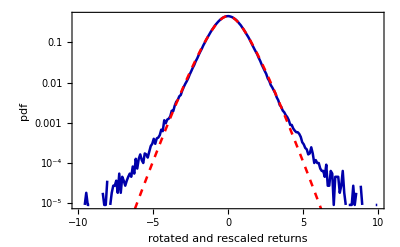

```mathematica
Show[ListLogPlot[Transpose[{xbins,hbins}],Joined->True,PlotRange->{{-10,10},All},PlotStyle->{Directive[Darker[Blue],Thickness[0.0045]]},Frame->True,FrameStyle->Directive[Thickness[0.0025],14], FrameLabel->{"rotated and rescaled returns","pdf"}],
LogPlot[pR[R,7,1],{R,-8,8},PlotStyle->{Red,Dashed,Thickness[0.0045]}]
]
```

```mathematica
Manipulate[Show[ListPlot[Transpose[{xbins,hbins}],Joined->True,PlotRange->{{-6,6},All},PlotStyle->{Directive[Darker[Blue],Thickness[0.0045]]},Frame->True,FrameStyle->Directive[Thickness[0.0025],14], FrameLabel->{"rotated and rescaled returns","pdf"}],
Plot[pR[R,M,1],{R,-6,6},PlotStyle->{Red,Dashed,Thickness[0.0045]},PlotRange->All]
],
{M,1,20,0.1}]
```

```mathematica
Manipulate[Show[ListLogPlot[Transpose[{xbins,HistogramList[Flatten@xdat⟦;;,k;;k+10⟧,{-10,10,0.1},"PDF"]⟦2⟧}],Joined->True,PlotRange->{{-10,10},All},PlotStyle->{Directive[Darker[Blue],Thickness[0.0045]]},Frame->True,FrameStyle->Directive[Thickness[0.0025],14], FrameLabel->{"rotated and rescaled returns","pdf"}],
LogPlot[pR[R,7,1],{R,-8,8},PlotStyle->{Red,Dashed,Thickness[0.0045]},PlotRange->All]
],
{k,1,414,1}]
```

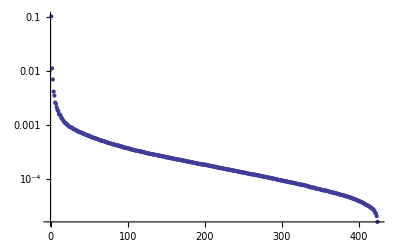

```mathematica
ListLogPlot[Eigenvalues@Covariance@rdat,PlotRange->All]
```

```mathematica
Eigenvalues@Covariance@rdat
```

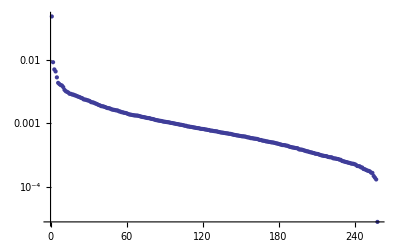

```mathematica
ListLogPlot[Eigenvalues@Covariance@Transpose@rdat2,PlotRange->All]
```

```mathematica
rdat2=Get["/data/finance/retNASDAQ.csv"];
```

```mathematica
Dimensions@rdat2
```

{258,5541}

```mathematica
First@rdat2
```

{{{0.019367991845056,,-0.012499999999999956,,0.,,-0.025316455696202556,}

```mathematica
xdat2=RotateAndScale@Transpose@rdat2;
```

```mathematica
Manipulate[Show[ListLogPlot[Transpose[{xbins,HistogramList[Flatten@xdat2⟦;;,k;;k+10⟧,{-10,10,0.1},"PDF"]⟦2⟧}],Joined->True,PlotRange->{{-10,10},All},PlotStyle->{Directive[Darker[Blue],Thickness[0.0045]]},Frame->True,FrameStyle->Directive[Thickness[0.0025],14], FrameLabel->{"rotated and rescaled returns","pdf"}],
LogPlot[pR[R,7,1],{R,-8,8},PlotStyle->{Red,Dashed,Thickness[0.0045]},PlotRange->All]
],
{k,1,248,1}]
```

```mathematica
Manipulate[Show[ListLogPlot[Transpose[{xbins,HistogramList[Flatten@xdat2⟦;;,k⟧,{-10,10,0.1},"PDF"]⟦2⟧}],Joined->True,PlotRange->{{-10,10},All},PlotStyle->{Directive[Darker[Blue],Thickness[0.0045]]},Frame->True,FrameStyle->Directive[Thickness[0.0025],14], FrameLabel->{"rotated and rescaled returns","pdf"}],
LogPlot[pR[R,7,1],{R,-8,8},PlotStyle->{Red,Dashed,Thickness[0.0045]},PlotRange->All]
],
{k,1,258,1}]
```

```mathematica
Partition[Range@10,4]
```

{{1,2,3,4},{5,6,7,8}}

```mathematica
Dimensions@rdat
```

{2565,424}

```mathematica
normalize[list_]:=(list-Mean@list)/StandardDeviation@list
```

```mathematica
pnormalize[list_,n_]:=Map[normalize,Partition[list,n]]
```

```mathematica
rdatn100=Transpose@Map[(Flatten@pnormalize[#,50])&,Transpose@rdat];
```

```mathematica
hl2=HistogramList[Flatten@rdatn100,{-10,10,0.1},"PDF"];
```

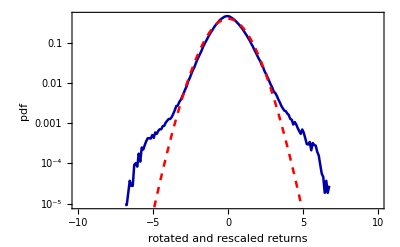

```mathematica
Show[ListLogPlot[Transpose[{xbins,hl2⟦2⟧}],Joined->True,PlotRange->{{-10,10},All},PlotStyle->{Directive[Darker[Blue],Thickness[0.0045]]},Frame->True,FrameStyle->Directive[Thickness[0.0025],14], FrameLabel->{"rotated and rescaled returns","pdf"}],
LogPlot[pR[R,60,1],{R,-8,8},PlotStyle->{Red,Dashed,Thickness[0.0045]}]
]
```